Negative energies

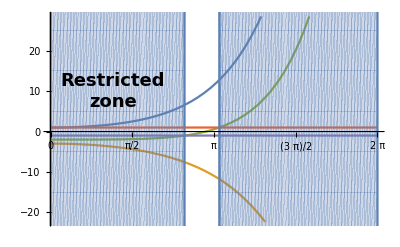

```mathematica
α=Rationalize[3];
rmax = 2*π;
equation = Cosh[x]-α*Sinh[x]/x;
p1 = Plot[{Cosh[x],-α*Sinh[x]/x, equation, 1, -1}, {x, 0, rmax},Ticks->{Range[0,rmax,Pi/2],Automatic}, ImageSize->Full];
regions = Reduce[Abs[equation] ≥  1&&0<x<rmax,x];
p2=RegionPlot[N[regions, 10], {x, 0, rmax}, {y, -500, 500}, PlotPoints->100];
text=Graphics[{Text[Style["Restricted\nzone",Bold,18],{1.2,10}]}];
Show[p1, p2, text]
```

Positive energies

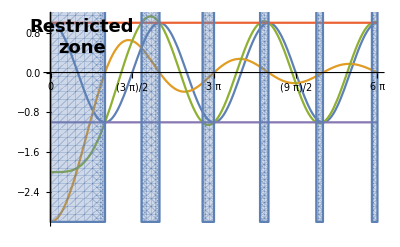

```mathematica
α=3;
rmax = 6*π;
equation = Cos[x]-α*Sin[x]/x;
p1 = Plot[{Cos[x],-α*Sin[x]/x, equation, 1, -1}, {x, 0, rmax},Ticks->{Range[0,rmax,Pi/2],Automatic}, ImageSize->Full];
regions = Reduce[Abs[equation] ≥  1&&0<x<rmax,x];
p2=RegionPlot[N[regions, 10], {x, 0, rmax}, {y, -3, 3}, PlotPoints->40];
text=Graphics[{Text[Style["Restricted\nzone",Bold,18],{1.8,0.7}]}];
Show[p1, p2, text]
```

E(K) plots

```mathematica
α=3;
rmax = Sqrt[240];
equation = Cos[x]-α*Sin[x]/x;
func[x_]:=ArcCos[equation];
positive = Quiet[ParametricPlot[{{func[x], x^2},{-func[x],x^2}}, {x, 0, rmax}, AspectRatio->2, ImageSize->400, Ticks->{Range[-π,π,Pi/4],Automatic}, AxesLabel->{"K","E"}]];
regions = Reduce[Abs[equation/.x->Sqrt[y]] ≥  1&&0<y<rmax^2,y];
positivezones = RegionPlot[regions,{x, -2*π, 2*π}, {y, 0, rmax^2}, PlotPoints->60];
```

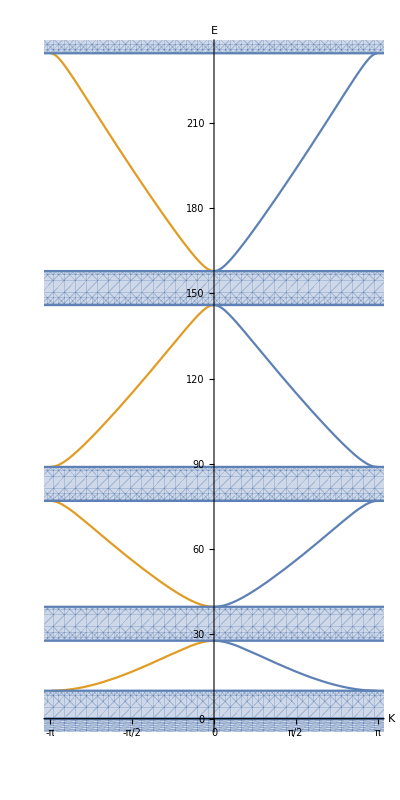

```mathematica
rmax = 6;
equation = Cosh[x]-α*Sinh[x]/x;
func[x_]:=ArcCos[equation];
negative = Quiet[ParametricPlot[{{func[x], -x^2},{-func[x],-x^2}}, {x, 0, rmax}]];
regions = Reduce[Abs[equation/.x->Sqrt[-y]] ≥  1&&-rmax^2<y<0,y];
negativezones = RegionPlot[regions,{x, -2*π, 2*π}, {y, -rmax^2, 0}, PlotPoints->60];
Show[positive, negative, positivezones, negativezones]
```